# Équation de Legendre

## Équation de Legendre

```mathematica
Legendre=(1-μ^2)P''[μ]-2μ P'[μ]+l(l+1)P[μ]==0;
```

```mathematica
DSolve[Legendre,P[μ],μ]//TraditionalForm
```

{{P(μ)→c_1 P_l(μ)+c_2 Q_l(μ)}}

## Les polynômes de Legendre de première espèce

### En coordonnées cartésiennes

```mathematica
l=4;
```

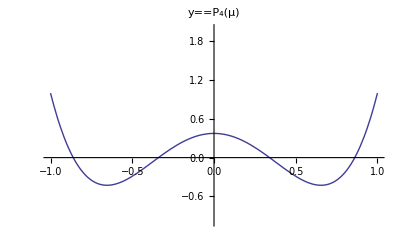

```mathematica
Plot[LegendreP[l,μ],{μ,-1,1},PlotRange->{{-1,1},{-1,2}},PlotLabel->Style[With[{l=l},HoldForm[y==LegendreP[l,μ]]],15]]
```

```mathematica
Clear[l]
```

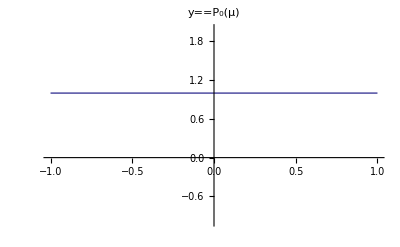
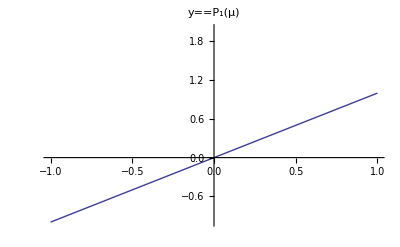
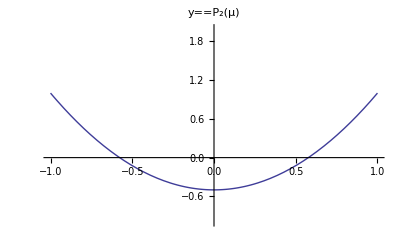
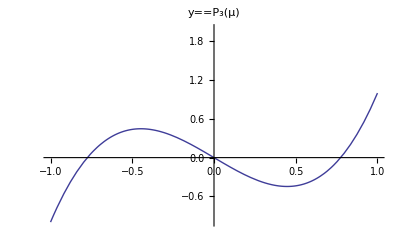
P_0(μ) | 1 | -Graphics-
P_1(μ) | μ | -Graphics-
P_2(μ) | 1/2 (3 μ^2-1) | -Graphics-
P_3(μ) | 1/2 (5 μ^3-3 μ) | -Graphics-
P_4(μ) | 1/8 (35 μ^4-30 μ^2+3) | -Graphics-

```mathematica
Grid[Table[{Style[With[{l=l},HoldForm[LegendreP[l,μ]]],15],LegendreP[l,μ],Plot[LegendreP[l,μ],{μ,-1,1},PlotRange->{{-1,1},{-1,2}},PlotLabel->Style[With[{l=l},HoldForm[y==LegendreP[l,μ]]],15]]},{l,0,4}],Frame->All]//TraditionalForm
```

### En coordonnées polaires

```mathematica
l=4;
```

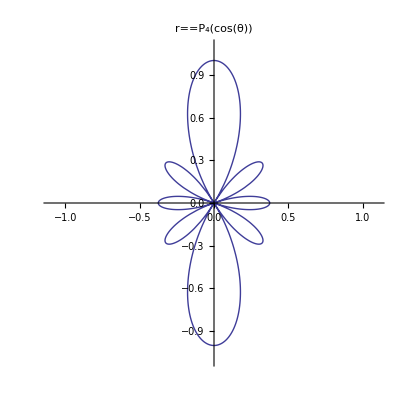

```mathematica
ParametricPlot[{Sin[θ],Cos[θ]}LegendreP[l,Cos[θ]],{θ,0,2π},PlotRange->1.1,PlotLabel->Style[With[{l=l},HoldForm[r==LegendreP[l,Cos[θ]]]],15]]
```

```mathematica
Clear[l]
```

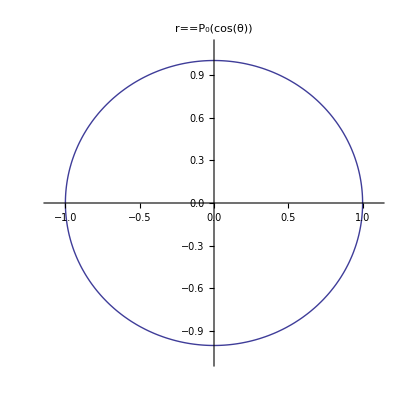
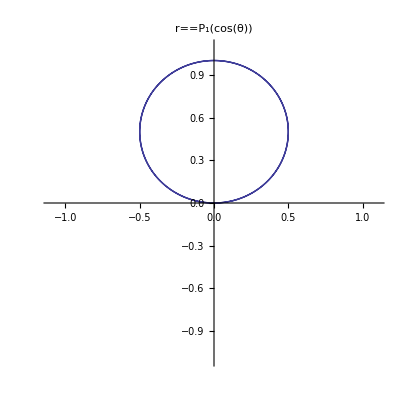
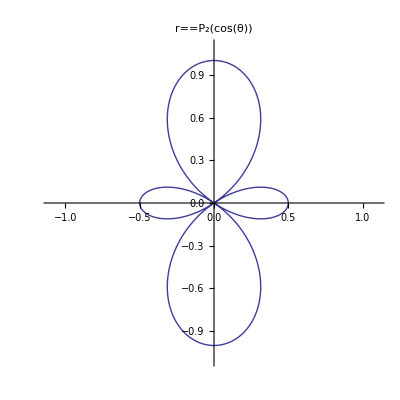
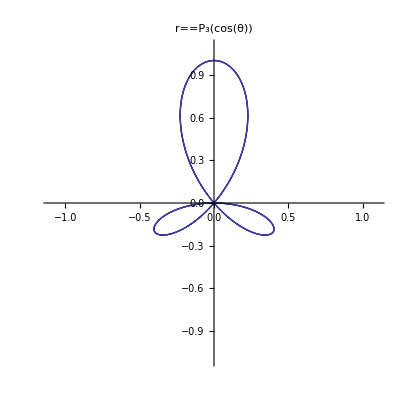
P_0(cos(θ)) | 1 | -Graphics-
P_1(cos(θ)) | cos(θ) | -Graphics-
P_2(cos(θ)) | 1/2 (3 cos^2(θ)-1) | -Graphics-
P_3(cos(θ)) | 1/2 (5 cos^3(θ)-3 cos(θ)) | -Graphics-
P_4(cos(θ)) | 1/8 (35 cos^4(θ)-30 cos^2(θ)+3) | -Graphics-

```mathematica
Grid[Table[{Style[With[{l=l},HoldForm[LegendreP[l,Cos[θ]]]],15],LegendreP[l,Cos[θ]],ParametricPlot[{Sin[θ],Cos[θ]}LegendreP[l,Cos[θ]],{θ,0,2π},PlotRange->1.1,PlotLabel->Style[With[{l=l},HoldForm[r==LegendreP[l,Cos[θ]]]],15]]},{l,0,4}],Frame->All]//TraditionalForm
```

## Formule de Rodriguez

```mathematica
l=3;
```

```mathematica
Subscript[P, l_][μ_]=1/(2^l l!)D[(μ^2-1)^l,{μ,l}];
```

```mathematica
Subscript[P, l][0.5]==LegendreP[l,0.5]
```

True

```mathematica
Clear[l]
```

## Parité

```mathematica
l=4;
```

```mathematica
LegendreP[l,-μ]==(-1)^l LegendreP[l,μ]
```

True

```mathematica
Clear[l]
```

## Relation d'orthonormalité

### En coordonnées cartésiennes

∫_-1^1 P_l(μ) P_l'(μ)ⅆμ=2/(2l+1)δ_ll'

```mathematica
l=3;l'=3;
```

```mathematica
∫_-1^1 LegendreP[l,μ]LegendreP[l',μ]ⅆμ
```

2/7

```mathematica
Clear[l]
```

### En coordonnées polaires

∫_0^π P_l(cosθ) P_l'(cosθ)sinθⅆμ=2/(2l+1)δ_ll'

```mathematica
l=3;l'=3;
```

```mathematica
∫_0^π LegendreP[l,Cos[θ]]LegendreP[l',Cos[θ]]Sin[θ]ⅆθ
```

2/7

```mathematica
Clear[l]
```

Donc, les polynômes  de Legendre de première espèce constituent une base complete,  c'est-à-dire qu'ils permettent de développer les fonctions f.

## La fonction à développer

```mathematica
f[x_]=2 x^5+x;
```

### Les coefficients

```mathematica
k=5;
```

```mathematica
coef=∫_-1^1 LegendreP[n,x]f[x]ⅆx;
```

```mathematica
c=Table[coef,{n,1,k}]
```

{26/21,0,16/63,0,32/693}

### Développement

```mathematica
k=5;
```

```mathematica
y[x_]=∑_(n=1)^k c[[n]]LegendreP[n,x]
```

(26 x)/21+8/63 (-3 x+5 x^3)+4/693 (15 x-70 x^3+63 x^5)

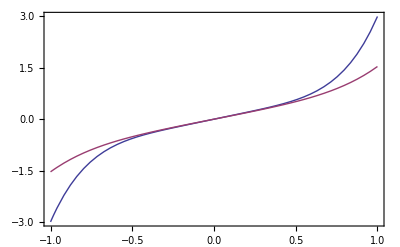

```mathematica
Plot[{f[x],y[x]},{x,-1,1},PlotRange->Full,Frame->True]
```

```mathematica
Clear[n]
```